```mathematica
Manipulate[Module[{sol,ACp,PDEp,cAMP,t},sol=NDSolve[{
ACp'[t]==r1*cAMP[t]*((ACt-ACp[t])/(K1))-r2*Dt*ACpt/(K2+ACpt+Dt),PDEp'[t]==r3*cAMP[t]*((PDEt-PDEp[t])/(K3))-r4*Et*(PDEpt)/(K4+PDEpt+Et),
cAMP'[t]==k1*(ACp[t])-(k2*PDE+k3)*cAMP[t],
ACp[0]==x0[[1]],PDEp[0]==x0[[2]],cAMP[0]==x0[[3]]},{ACp,PDEp,cAMP},{t,0,500}];
Plot[Evaluate[{ACp[t],PDEp[t],cAMP[t]}/. sol],{t,0,500},PlotRange->All,PlotLegends->{"ACp(t)","PDEp(t)","cAMP(t)"},AxesLabel->{"Time","Concentration"}]],
{{k1,2.85},0,10,Appearance->"Labeled"},
{{PDE,2.85},0,10,Appearance->"Labeled"},
{{ACpt,2.85},0,10,Appearance->"Labeled"},
{{k2,2.85},0,10,Appearance->"Labeled"},
{{PDEpt,2.85},0,10,Appearance->"Labeled"},
{{k3,0.69},0,10,Appearance->"Labeled"},
{{k4,4.45},0,10,Appearance->"Labeled"},
{{r1,0.52},0,10,Appearance->"Labeled"},
{{r2,0.47},0,10,Appearance->"Labeled"},
{{r3,2},0,10,Appearance->"Labeled"},
{{r4,10},0,10,Appearance->"Labeled"},
{{Et,0.28},0,10,Appearance->"Labeled"},
{{Dt,0.15},0,10,Appearance->"Labeled"},
{{K1,0.1},0,10,Appearance->"Labeled"},
{{K2,0.1},0,10,Appearance->"Labeled"},
{{K3,0.001},0,10,Appearance->"Labeled"},
{{K4,1},0,10,Appearance->"Labeled"},
{{ACt,0},0,10,Appearance->"Labeled"},
{{PDEt,0},0,10,Appearance->"Labeled"},{{x0,{0.33,0.33,0.33}},Appearance->"Labeled"},Button["Randomize Parameters",
k1=RandomReal[{0,10}];
PDE=RandomReal[{0,10}];
ACpt=RandomReal[{0,10}];
PDEpt=RandomReal[{0,10}];
k2=RandomReal[{0,10}];
k3=RandomReal[{0,10}];
k4=RandomReal[{0,10}];
r1=RandomReal[{0,10}];
r2=RandomReal[{0,10}];
r3=RandomReal[{0,10}];
r4=RandomReal[{0,10}];
Et=RandomReal[{0,10}];
Dt=RandomReal[{0,10}];
K1=RandomReal[{0,10}];
K2=RandomReal[{0,10}];
K3=RandomReal[{0,10}];
K4=RandomReal[{0,10}];
ACt=RandomReal[{0,10}];
PDEt=RandomReal[{0,10}]],TrackedSymbols->{k2,k1,k3,k4,r1,r2,r3,r4,Et,Dt,K1,K2,K3,K4,ACpt,PDEpt,PDE,x0}
]
```

General::munfl: 1/(5.16482×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.12691×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(7.2687×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NDSolve::ndsz: At t$376220 == 8.05439, step size is effectively zero; singularity or stiff system suspected.

General::munfl: 1/(4.75594×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.65285×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.72083×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NDSolve::ndsz: At t$377116 == 1.70885, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$377734 == 1.87315, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$377856 == 0.60861, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$378758 == 4.60897, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$378880 == 2.15736, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$379002 == 2.31394, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$379702 == 2.50997, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$380880 == 10.5608, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$381002 == 0.551879, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$381988 == 4.20799, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$382110 == 0.865935, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$383396 == 1.58367, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$384904 == 0.88015, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$385866 == 1.66271, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$385988 == 0.819603, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$387238 == 0.266788, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$388176 == 0.587608, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$388970 == 4.15317, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$389092 == 0.879598, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$390354 == 44.1492, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$390476 == 2.72341, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$392034 == 6.02102, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$442512 == 6.57533, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$457548 == 2.26008, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$459930 == 2.26008, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$460052 == 1.85181, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$460900 == 5.77716, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$461402 == 17.9705, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$461524 == 8.73114, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$461646 == 0.796672, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$462908 == 7.73284, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$463208 == 3.01956, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t$463330 == 3.38326, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t$646324 == 37.1571; unable to continue.

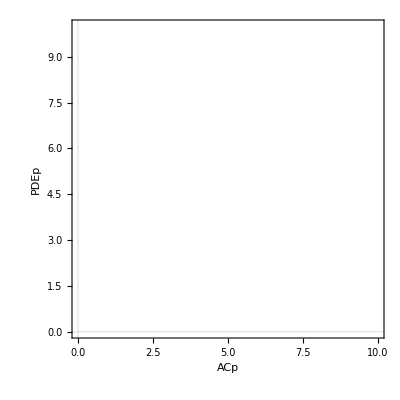

```mathematica
(*Constants*)r1=0.98;r2=4.48;r3=1;r4=1;
K1=1;K2=1;K3=1;K4=1;
k1=1;k3=1;k4=1;
ACt=1;PDEt=1;Dval=1;Evalue=1;

(*ODEs*)odeACp=r1*camp*((ACt-ACp)/(K1))-r2*Dvalue*ACp/(K2+ACp);
odePDEp=r3*camp*((PDEt-PDEp)/(K3))-r4*Evalue*(PDEp)/(K4+PDEp);
odecAMP=(k1*(ACp))-(k3+k4*(PDEp))*camp;

(*Nullcline Equations*)
nullclineACp=odeACp==0;
nullclinePDEp=odePDEp==0;
nullclinecAMP=odecAMP==0;

(*Eliminate camp from nullcline equations*)
eliminatedEquation=Eliminate[{nullclineACp,nullclinePDEp,nullclinecAMP},camp];

(*Plotting the nullclines*)
ContourPlot[Evaluate[eliminatedEquation],{ACp,0,10},{PDEp,0,10},FrameLabel->{"ACp","PDEp"},PlotTheme->"Scientific",ContourStyle->{Red,Green,Blue}]
```